# Hermitian Hamiltonian Eigenvalues (2-level system)

## This part, I used the simple Hermitian matrix as demonstration and can be used as comparison for the NHH case which is demonstrated later. The eigenvalue is modelled as . The mixing of the state is calculated using .

```mathematica
(*This is when the hamiltonian is hermitian*)
ClearAll["Global`*"]

(*Define the eigenvalue functions for the 2×2 Hamiltonian*)
Eplus[delta_,omega_]:=(-delta/2+Sqrt[omega^2+delta^2])/2;
Eminus[delta_,omega_]:=(-delta/2-Sqrt[omega^2+delta^2])/2;

(*In our case,we set gam=0 so that z=Δ₂ is real.We will let d denote Δ₂ and x denote Ω.*)
(*Define the mixing (ground state projection) for each eigenstate*)
mixingEplus[delta_,omega_]:=(1-delta/Sqrt[delta^2+omega^2])/2;
mixingEminus[delta_,omega_]:=(1+delta/Sqrt[delta^2+omega^2])/2;

(*Plot settings:note that the ranges below are as given in your code;
they are quite large,so adjust if necessary.*)

plotEplus=Plot3D[Re[Eplus[delta,omega]],{delta,-3*10^6*2*Pi,3*10^6*2*Pi},{omega,-2*10^7,2*10^7},PlotRange->All,PlotStyle->Directive[Opacity[0.8]],ColorFunction->Function[{delta,omega,z},ColorData["Rainbow"][mixingEplus[delta,omega]]],ColorFunctionScaling->False,Mesh->Automatic,MeshStyle->Directive[Gray,Thin],Lighting->"Neutral",Axes->True,AxesLabel->{Subscript["Δ",2]" (rad/s)","Ω (rad/s)","E"},AxesStyle->Thick,BoxRatios->{1,1,1},PlotLegends->BarLegend[{ColorData["Rainbow"],{0,1}},LabelStyle->{Bold,12},LegendLabel->"Exci. Prob."]];

plotEminus=Plot3D[Re[Eminus[delta,omega]],{delta,-3*10^6*2*Pi,3*10^6*2*Pi},{omega,-2*10^7,2*10^7},PlotRange->All,PlotStyle->Directive[Opacity[0.8]],ColorFunction->Function[{delta,omega,z},ColorData["Rainbow"][mixingEminus[delta,omega]]],ColorFunctionScaling->False,Mesh->Automatic,MeshStyle->Directive[Gray,Thin],Lighting->"Neutral"];

(*Combine the two surfaces into one 3D view*)
Show[plotEplus,plotEminus]
```

-Graphics3D-

# Non-Hermitian Hamiltonian Eigenvalues/Eigenvectors (2-level system)

## Eigenvalues (Real part and Imaginary part)

### NHH gives some unexpected eigenvalues. First of all, the eigenvalues are complex, and there’s a special line where the real parts of the eigenvalues coalesce, indicating an exceptional point. The code calculates these eigenvalues, and , for a non-Hermitian Hamiltonian and visualizes the real and imaginary parts of both surfaces using 3D plots. The plots reveal how the eigenvalues depend on system parameters, showing the characteristic branching structure typical of non-Hermitian systems. Here, I put some real experiment values for the two level system under a laser (L2) depletion. [gam = decay rate; d = L2 detuning; x = Rabi frequency = ]

```mathematica
(*This is when the hamiltonian is non-hermitian*)
ClearAll["Global`*"]
Eplus[z_,x_]:=(z+Sqrt[4x^2+z^2])/2;
Eminus[z_,x_]:=(z-Sqrt[4x^2+z^2])/2;
gam=2.7 10^6 2Pi; 

(*First surface:real part of Eplus*)plotEplus=Plot3D[Re[Eplus[d-I*gam/2,x]],{d,-3 10^6 2Pi,3 10^6 2Pi},{x,-10^7, 10^7},PlotRange->All,PlotStyle->Directive[Gray,Opacity[0.5]],(*no surface shading*)Mesh->Automatic,(*show mesh lines*)MeshStyle->Directive[Gray,Thin],(*gray,thin wireframe*)Lighting->"Neutral",(*avoid shading effects*)Axes->True,AxesLabel->{"(rad/s)","(rad/s)","Re(E)"},AxesStyle->Thick,BoxRatios->{1,1,1}];

(*Second surface:real part of Eminus*)
plotEminus=Plot3D[Re[Eminus[d-I*gam/2,x]],{d,-3 10^6 2Pi,3 10^6 2Pi},{x,-10^7, 10^7},PlotRange->All,PlotStyle->Directive[Gray,Opacity[0.5]],Mesh->Automatic,MeshStyle->Directive[Gray,Thin],Lighting->"Neutral",Axes->True,AxesLabel->{"(rad/s)","(rad/s)","Re(E)"},AxesStyle->Thick,BoxRatios->{1,1,1}];

(*Combine both surfaces into one 3D view*)
Show[plotEplus,plotEminus]
```

-Graphics3D-

```mathematica
plotEplusImag=Plot3D[Im[Eplus[d-I*gam/2,x]],{d,-3 10^6 2Pi,3 10^6 2Pi},{x,0, 10^7},PlotRange->All,PlotStyle->Directive[Gray,Opacity[0.5]],(*no surface shading*)Mesh->Automatic,(*show mesh lines*)MeshStyle->Directive[Gray,Thin],(*gray,thin wireframe*)Lighting->"Neutral",(*avoid shading effects*)Axes->True,AxesLabel->{"(rad/s)","(rad/s)","Im(E)"},AxesStyle->Thick,BoxRatios->{1,1,1}];

(*Second surface:real part of Eminus*)
plotEminusImag=Plot3D[Im[Eminus[d-I*gam/2,x]],{d,-3 10^6 2Pi,3 10^6 2Pi},{x,0, 10^7},PlotRange->All,PlotStyle->Directive[Gray,Opacity[0.5]],Mesh->Automatic,MeshStyle->Directive[Gray,Thin],Lighting->"Neutral",Axes->True,AxesLabel->{"(rad/s)","(rad/s)","Im(E)"},AxesStyle->Thick,BoxRatios->{1,1,1}];

(*Combine both surfaces into one 3D view*)
Show[plotEplusImag,plotEminusImag]
```

-Graphics3D-

## Eigenvectors

### Similarly, eigenvector of the NHH is also kinda strange: It’s not necessarily orthogonal to each other (only biorthogonal). This effect can be seen around the exceptional point, where at the exceptional point (EP), the two eigenvectors are actually colinear, which corresponds to where the eigenvalues coincide. This can be shown by plotting the overlap between the two eigenvectors (both left or both right) around the EP. In this part, I calculated the normalized left/right eigenvectors, then I plot the overlap behavior of the eigenvectors around the EP of a demo NHH.

```mathematica
ClearAll["Global`*"]
M={{0,x},{x,z}};

(* Compute the right and left eigenvalues/eigenvectors*)
{valsR,vecsR}=Eigensystem[M];
{valsL,vecsL}=Eigensystem[ConjugateTranspose[M]];

(* Print normalized eigenvectors*)
Do[
Module[
{vR,vL,overlap,normR,normL},
vR=vecsR[[i]];
vL=vecsL[[i]];

(* Compute the overlap and normalize*)
overlap=ConjugateTranspose[vL].vR;
normR=vR/Sqrt[overlap];
normL=vL/Sqrt[Conjugate[overlap]];

(* Print results*)
Print["Eigenvalue: ",valsR[[i]]];
Print["  Normalized Right vector: ",normR];
Print["  Normalized Left vector:  ",normL];
Print["-----------------------------------"];
],
{i,1,Length[valsR]}
];
```

Eigenvalue: 1/2 (z-√(4 x^2+z^2))

Normalized Right vector: {-(z+√(4 x^2+z^2))/(2 x √(1+((z+√(4 x^2+z^2)) (z+Conjugate[√(4 Conjugate[x]^2+Conjugate[z]^2)]))/(4 x^2))),1/(√(1+((z+√(4 x^2+z^2)) (z+Conjugate[√(4 Conjugate[x]^2+Conjugate[z]^2)]))/(4 x^2)))}

Normalized Left vector:  {-(Conjugate[z]+√(4 Conjugate[x]^2+Conjugate[z]^2))/(2 Conjugate[x] √(1+((Conjugate[z]+√(4 Conjugate[x]^2+Conjugate[z]^2)) Conjugate[z+√(4 x^2+z^2)])/(4 Conjugate[x]^2))),1/(√(1+((Conjugate[z]+√(4 Conjugate[x]^2+Conjugate[z]^2)) Conjugate[z+√(4 x^2+z^2)])/(4 Conjugate[x]^2)))}

-----------------------------------

Eigenvalue: 1/2 (z+√(4 x^2+z^2))

Normalized Right vector: {-(z-√(4 x^2+z^2))/(2 x √(1+((z-√(4 x^2+z^2)) (z-Conjugate[√(4 Conjugate[x]^2+Conjugate[z]^2)]))/(4 x^2))),1/(√(1+((z-√(4 x^2+z^2)) (z-Conjugate[√(4 Conjugate[x]^2+Conjugate[z]^2)]))/(4 x^2)))}

Normalized Left vector:  {-(Conjugate[z]-√(4 Conjugate[x]^2+Conjugate[z]^2))/(2 Conjugate[x] √(1+((Conjugate[z]-√(4 Conjugate[x]^2+Conjugate[z]^2)) (Conjugate[z]-Conjugate[√(4 x^2+z^2)]))/(4 Conjugate[x]^2))),1/(√(1+((Conjugate[z]-√(4 Conjugate[x]^2+Conjugate[z]^2)) (Conjugate[z]-Conjugate[√(4 x^2+z^2)]))/(4 Conjugate[x]^2)))}

-----------------------------------

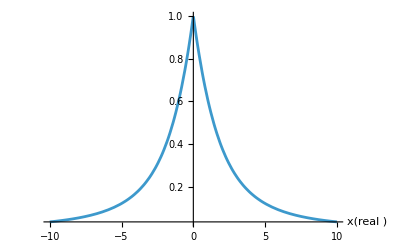

```mathematica
ClearAll["Global`*"]
(*Define M as a function of real parameter x,so that z=-2 I+x.*)
M[x_]:={{0,1},{1,-2I+x}};

(*Define a function that returns the overlap between the two right eigenvectors of M[x].*)
overlapOfEigenvectors[x_]:=Module[{vals,vecs,ov},(*Get eigenvalues and (right) eigenvectors of M[x].*)
{vals,vecs}=Eigensystem[M[x]];
(*In Mathematica,vecs[[1]] and vecs[[2]] are column vectors.The usual “bra-ket” overlap is v1^\dagger v2,which is ConjugateTranspose[v1].v2 in Mathematica.*)
ov=ConjugateTranspose[vecs[[1]]].vecs[[2]];
(*Return that overlap.*)ov];
Plot[Abs[overlapOfEigenvectors[x]],{x,-10,10},PlotRange->All,AxesLabel->{"x(real )",""}]
```

```mathematica
overlap[x_,y_]:=Module[{mat,vals,vecs,ov},
(*z=-2I+δ*)
mat={{0,1},{1,(x+I y)}};
(*Compute right eigenvalues and eigenvectors*)
{vals,vecs}=Eigensystem[mat];
(*Compute the overlap between the two eigenvectors*)
ov=ConjugateTranspose[vecs[[1]]].vecs[[2]];
ov
];

(*Plot the absolute value of the overlap in 3D*)
Plot3D[
Abs[overlap[x,y]],
{x,-5,5},{y,-10,10},
AxesLabel->{"Re(z)","Im(z)","|Overlap|"},
PlotRange->All,
Mesh->None,
ColorFunction->"Rainbow",
PlotLabel->"Absolute Overlap vs. z"
]
```

-Graphics3D-

## Exceptional Point

### The exceptional point is found when the eigenenergies degenerate, which occurs when the stuff under the square root vanishes

```mathematica
Clear[x,y,a]
Solve[4 x^2+(y-I a/2)^2==0&&Element[{x,y,a},Reals],{x,y}]
```

{{x→ConditionalExpression[-(√(a^2))/4, a∈ℝ],y→ConditionalExpression[0, a∈ℝ]},{x→ConditionalExpression[(√(a^2))/4, a∈ℝ],y→ConditionalExpression[0, a∈ℝ]}}

## 2-Level system Laser Depletion using non-Hermitian Berry phase approach (actually, there’s no geometric phase)

### Assumptions: 1. Adiabatic; 2. initial state is (1,0). This uses the berry phase formula brought up in one of the paper. The model is a two level system with a depletion laser L2, initially populated at the stable level, this formula only correctly gives the population after exactly one cycle is complete. However, since we only move along a line in parameter space, we didn’t actually enclose any area inside this parameter space, so the Barry phase should be 0. This is just to give an example usage of this formula and to see if this correctly describe the depletion behavior.

```mathematica
ClearAll["Global`*"]

(*Parameters*)
Delta2=3 10^6 2 Pi;
gamma=2.7 10^6 2Pi;
c=1000;
sigma=0.52 10^(-6);
t0=52.6 10^(-6);  (*Center of the Gaussian*)

(*Define the Gaussian coupling profile*)
Omega[t_]:= c * Exp[-(t-t0)^2/(2 sigma^2)]/2;

(*Define the eigenvalue λ₊(t) expanded*)
lambdaPlus[t_]:=(Delta2-I gamma/2+Sqrt[(Delta2-I gamma/2)^2+4 Omega[t]^2])/2;
lambdaMinus[t_]:=(Delta2-I gamma/2-Sqrt[(Delta2-I gamma/2)^2+4 Omega[t]^2])/2;

(*Compute the dynamic phase φ as the integral from-∞ to ∞*)
phi=-I Integrate[lambdaPlus[t],{t,-51.1 10^(-6),200 10^(-6)},Assumptions->{sigma>0,c>0}];
phiMinus=-I Integrate[lambdaMinus[t],{t,-51.1 10^(-6),200 10^(-6)},Assumptions->{sigma>0,c>0}];

(*Compute the evolution factor f=exp(φ)*)
evolutionFactor=Abs[Exp[phi]]^2;
evolutionFactorminus=Abs[Exp[phiMinus]]^2;
{phi,phiMinus}
{evolutionFactor,evolutionFactorminus}
```

General::munfl: Exp[-2129.91-4733.12 ⅈ] is too small to represent as a normalized machine number; precision may be lost.

{-2129.91-4733.12 ⅈ,7.01565×10^-13+1.40313×10^-12 ⅈ}

{0.,1.}

NIntegrate::pvrng: Singular points must be specified in the integration range in order to use PrincipalValue.

Integral result = NIntegrate[integrand[t],{t,t1,t2},Method→PrincipalValue]

## This part calculates the eigenvalues and eigenvectors of the 3 by 3 non-Hermitian Hamiltonian in our case

```mathematica
(*Clear previous definitions*)ClearAll[d12,E0,omega,d13,E_L2,E0nr,t0L2,t0nr,sigma,Delta1,Delta2,gamma,t];

(*Parameter Definitions*)
d12=-33.6*2*Pi;         (*dipole moment for 1-2 (arbitrary units)*)
E0=40;                (*field amplitude for 1-2 transition*)
omega=2*Pi*11.44*10^3;    (*angular frequency for the sine field*)

d13=-2.15*10^4*2*Pi;    (*dipole moment for 1-3 transition*)
EL2=8.514*10^2;         (*electric field amplitude for L2*)
E0nr=12;                 (*additional amplitude for non-resonant part*)
t0L2=52.6*10^-6;         (*center of the Gaussian pulse (s)*)
t0nr=70.1*10^-6;         (*center of the non-resonant term (s)*)
sigma=0.52*10^-6;         (*pulse width (s)*)

Delta1=2*Pi*2*10^3;       (*detuning for state 2 (1-2 transition)*)
Delta2=2*Pi*1*10^6*3;     (*detuning for state 3 (L2 detuning)*)
gamma=2.7*10^6*2*Pi;      (*decay rate for state 3*)

(*Define the time-dependent coupling functions*)

(*EStark is active only when-43.7 µs<t<43.7 µs*)
EStark[t_]:=Piecewise[{{d12*E0*Sin[omega*(t+43.7*10^-6)],-43.7*10^-6<t<43.7*10^-6}},0];

(*Non-resonant coupling*)
Enr[t_]:=d12*E0nr*Sech[616*(t-t0nr)/(0.76*10^-2)];

(*Combined coupling for the 1-2 transition*)
Omega[t_]:=EStark[t]+Enr[t];

(*1-3 coupling:Gaussian pulse*)
Omega13prime[t_]:=0.5*d13*EL2*Exp[-((t-t0L2)^2)/(2*sigma^2)];

(*Define the 3x3 non-Hermitian Hamiltonian H(t)*)
H[t_]:={{0,Omega[t],Omega13prime[t]},{Omega[t],Delta1,0},{Omega13prime[t],0,Delta2-I*(gamma/2)}};

(*Function to compute the eigenvalues and eigenvectors at a specific time t0*)
eigensystemAtTime[t0_?NumericQ]:=Eigensystem[H[t0]];

(*Compute the eigenvalues and eigenvectors at t=43.7 µs*)
tValue=54.99*10^-6;
Print["Hamiltonian at t = ",tValue," seconds:"];
MatrixForm[H[tValue]]
{eigenValues,eigenVectors}=eigensystemAtTime[tValue];

(*Function to format a complex number as "real + i imag"*)
formatComplex[z_]:=Module[{a=N[Re[z]],b=N[Im[z]]},a+I*b];

(*Apply formatting to each eigenvalue and eigenvector element*)
formattedEigenValues=formatComplex/@eigenValues;
formattedEigenVectors=Map[formatComplex,eigenVectors,{2}];

(*Output the results*)
Print["At t = ",tValue," seconds:"];
Print["Eigenvalues (real + i imag): ",formattedEigenValues];
Print["Eigenvectors (real + i imag): ",formattedEigenVectors];
```

Hamiltonian at t = 0.00005499 seconds:

(0 | -1370.5 | -1487.88
-1370.5 | 4000 π | 0
-1487.88 | 0 | 1.88496×10^7-8.4823×10^6 ⅈ)

At t = 0.00005499 seconds:

Eigenvalues (real + i imag): {1.88496×10^7-8.4823×10^6 ⅈ,12714.1-0.000505374 ⅈ,-147.829-0.0434447 ⅈ}

Eigenvectors (real + i imag): {{-0.0000656418-0.0000295388 ⅈ,3.16609×10^-9+3.57482×10^-9 ⅈ,1.+0. ⅈ},{-0.107172+3.66626×10^-7 ⅈ,0.99424+0. ⅈ,-7.03814×10^-6-3.16927×10^-6 ⅈ},{0.99424+0. ⅈ,0.107172-3.6621×10^-7 ⅈ,0.0000652634+0.0000293683 ⅈ}}

## Calculate evolution operator of our time dependent nHH

```mathematica
(*Clear previous definitions*)ClearAll[d12,E0,omega,d13,E_L2,E0nr,t0L2,t0nr,sigma,Delta1,Delta2,gamma,t];

(*Parameter Definitions*)
d12=-33.6*2*Pi;         (*dipole moment for 1-2 (arbitrary units)*)
E0=40;                (*field amplitude for 1-2 transition*)
omega=2*Pi*11.44*10^3;    (*angular frequency for the sine field*)

d13=-2.15*10^4*2*Pi;    (*dipole moment for 1-3 transition*)
EL2=8.514*10^2;         (*electric field amplitude for L2*)
E0nr=12;                 (*additional amplitude for non-resonant part*)
t0L2=52.6*10^-6;         (*center of the Gaussian pulse (s)*)
t0nr=70.1*10^-6;         (*center of the non-resonant term (s)*)
sigma=0.52*10^-6;         (*pulse width (s)*)

Delta1=2*Pi*2*10^3;       (*detuning for state 2 (1-2 transition)*)
Delta2=2*Pi*1*10^6*3;     (*detuning for state 3 (L2 detuning)*)
gamma=2.7*10^6*2*Pi;      (*decay rate for state 3*)

(*Define the time-dependent coupling functions*)

(*EStark is active only when-43.7 µs<t<43.7 µs*)
EStark[t_]:=Piecewise[{{d12*E0*Sin[omega*(t+43.7*10^-6)],-43.7*10^-6<t<43.7*10^-6}},0];

(*Non-resonant coupling*)
Enr[t_]:=d12*E0nr*Sech[616*(t-t0nr)/(0.76*10^-2)];

(*Combined coupling for the 1-2 transition*)
Omega[t_]:=EStark[t]+Enr[t];

(*1-3 coupling:Gaussian pulse*)
Omega13prime[t_]:=0.5*d13*EL2*Exp[-((t-t0L2)^2)/(2*sigma^2)];

(*Define the 3x3 non-Hermitian Hamiltonian H(t)*)
H[t_]:={{0,Omega[t],Omega13prime[t]},{Omega[t],Delta1,0},{Omega13prime[t],0,Delta2-I*(gamma/2)}};

(*Define the differential equation for U(t) with U(0)=IdentityMatrix[3]*)
eqn=D[U[t],t]==-I*H[t].U[t];
initialCondition=U[-43.7*10^-6]==IdentityMatrix[3];

(*Solve the differential equation numerically from t=0 to t=1*)
sol=NDSolve[{eqn,initialCondition},U,{t,-43.7*10^-6,150*10^-6}];

(*Extract the solution at t=1*)
U1td=U[55.3*10^-6]/. sol[[1]];

Print["The time-dependent evolution operator U(1,0) is:"];
MatrixForm[U1td]
```

The time-dependent evolution operator U(1,0) is:

(0.00133747-0.00164674 ⅈ | 0.00206224+0.00121697 ⅈ | -1.21146×10^-21-4.34398×10^-21 ⅈ
0.0977715-0.0659731 ⅈ | 0.336873-0.93413 ⅈ | 3.77741×10^-22+3.52111×10^-21 ⅈ
5.24431×10^-9-7.50224×10^-9 ⅈ | 9.17015×10^-9+4.88565×10^-9 ⅈ | -6.69145×10^-27-1.80978×10^-26 ⅈ)

```mathematica
(*Define the time variables*)
t0=-43.7*10^-6;  (*initial time*)
tF=t; (*final time remains symbolic*)

(*Zeroth-order term:identity matrix*)
U0=IdentityMatrix[3];

(*First-order term*)
U1=-I Integrate[H[t1],{t1,t0,tF}];

(*Second-order term*)
U2=(-I)^2 Integrate[Integrate[H[t1].H[t2],{t2,t0,t1}],{t1,t0,tF}];

(*Dyson series expansion up to second order*)
Upert[t_]:=U0+U1+U2;

(*Evaluate and simplify the evolution operator at t=1*)
result=Simplify[Upert[t_]];

(*Print the matrix form at t=1*)
Print["The Dyson series approximation for U(t) at t is:"];
MatrixForm[result]
```

The Dyson series approximation for U(t) at t is:

(1-ⅈ ∫_-0.0000437^t H[t1]ⅆt1-∫_-0.0000437^t (∫_-0.0000437^t1 H[t1].H[t2]ⅆt2)ⅆt1 | -ⅈ ∫_-0.0000437^t H[t1]ⅆt1-∫_-0.0000437^t (∫_-0.0000437^t1 H[t1].H[t2]ⅆt2)ⅆt1 | -ⅈ ∫_-0.0000437^t H[t1]ⅆt1-∫_-0.0000437^t (∫_-0.0000437^t1 H[t1].H[t2]ⅆt2)ⅆt1
-ⅈ ∫_-0.0000437^t H[t1]ⅆt1-∫_-0.0000437^t (∫_-0.0000437^t1 H[t1].H[t2]ⅆt2)ⅆt1 | 1-ⅈ ∫_-0.0000437^t H[t1]ⅆt1-∫_-0.0000437^t (∫_-0.0000437^t1 H[t1].H[t2]ⅆt2)ⅆt1 | -ⅈ ∫_-0.0000437^t H[t1]ⅆt1-∫_-0.0000437^t (∫_-0.0000437^t1 H[t1].H[t2]ⅆt2)ⅆt1
-ⅈ ∫_-0.0000437^t H[t1]ⅆt1-∫_-0.0000437^t (∫_-0.0000437^t1 H[t1].H[t2]ⅆt2)ⅆt1 | -ⅈ ∫_-0.0000437^t H[t1]ⅆt1-∫_-0.0000437^t (∫_-0.0000437^t1 H[t1].H[t2]ⅆt2)ⅆt1 | 1-ⅈ ∫_-0.0000437^t H[t1]ⅆt1-∫_-0.0000437^t (∫_-0.0000437^t1 H[t1].H[t2]ⅆt2)ⅆt1)

```mathematica
ClearAll[H,Omega13,Delta2,gamma,t,lambda];

(*Define the Hamiltonian H(t)*)
H[t_]:={{0,Omega13[t]},{Omega13[t],Delta2-I*gamma/2}};

(*Method 1:Directly use Eigenvalues*)
eigVals=Eigenvalues[H[t]]//Simplify

(*Method 2:Solve the characteristic polynomial explicitly*)
eigSol=Solve[Det[H[t]-lambda IdentityMatrix[2]]==0,lambda]//Simplify

(*The output from either method will be:lambda->(Delta2-I Gamma/2-Sqrt[(Delta2-I Gamma/2)^2+4 Omega13[t]^2])/2 and lambda->(Delta2-I Gamma/2+Sqrt[(Delta2-I Gamma/2)^2+4 Omega13[t]^2])/2*)
```

{1/4 (2 Delta2-ⅈ gamma-√((2 Delta2-ⅈ gamma)^2+16 Omega13[t]^2)),1/4 (2 Delta2-ⅈ gamma+√((2 Delta2-ⅈ gamma)^2+16 Omega13[t]^2))}

{{lambda→1/4 (2 Delta2-ⅈ gamma-√((2 Delta2-ⅈ gamma)^2+16 Omega13[t]^2))},{lambda→1/4 (2 Delta2-ⅈ gamma+√((2 Delta2-ⅈ gamma)^2+16 Omega13[t]^2))}}

```mathematica
Series[Sqrt[1+x],{x,0,4}]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+O[x]^5

## Map Analytical Form of Asymmetry to the fitting function

```mathematica
(*Clear any previous definitions for the variables*)Clear[Delta,K1,K4,E0nr,a,phi,K3,Γ,Delta2,T];

(*Define the analytic asymmetry function A[Delta]*)
A[Delta_]:=(-2*K1*K4*E0nr*Sin[Delta*phi]*Exp[-Delta^2/(4*a)]*Exp[(K3*Γ/2)/(Delta2^2+(Γ/2)^2)]*Sin[Delta*(T-phi)-(K3*Delta2)/(Delta2^2+(Γ/2)^2)])/(K1^2*Sin[Delta*phi]^2+E0nr^2*K4^2*Exp[-Delta^2/(2*a)]*Exp[(K3*Γ)/(Delta2^2+(Γ/2)^2)]);

(*Compute the power-series expansion of A[Delta] about Delta=0 up to order 2*)
seriesExpansion=Series[A[Delta],{Delta,0,2}];

(*Display the result*)
Normal[seriesExpansion]
```

-(2 Delta^2 ⅇ^(-(2 K3 Γ)/(4 Delta2^2+Γ^2)) K1 phi (-phi+T) Cos[(4 Delta2 K3)/(4 Delta2^2+Γ^2)])/(E0nr K4)-(Delta^4 ⅇ^(-(6 K3 Γ)/(4 Delta2^2+Γ^2)) K1 phi (phi-T) (-3 ⅇ^((4 K3 Γ)/(4 Delta2^2+Γ^2)) E0nr^2 K4^2+12 a K1^2 phi^2+4 a ⅇ^((4 K3 Γ)/(4 Delta2^2+Γ^2)) E0nr^2 K4^2 phi^2-4 a ⅇ^((4 K3 Γ)/(4 Delta2^2+Γ^2)) E0nr^2 K4^2 phi T+2 a ⅇ^((4 K3 Γ)/(4 Delta2^2+Γ^2)) E0nr^2 K4^2 T^2) Cos[(4 Delta2 K3)/(4 Delta2^2+Γ^2)])/(6 a E0nr^3 K4^3)+(2 Delta ⅇ^(-(2 K3 Γ)/(4 Delta2^2+Γ^2)) K1 phi Sin[(4 Delta2 K3)/(4 Delta2^2+Γ^2)])/(E0nr K4)-(Delta^3 ⅇ^(-(6 K3 Γ)/(4 Delta2^2+Γ^2)) K1 phi (-3 ⅇ^((4 K3 Γ)/(4 Delta2^2+Γ^2)) E0nr^2 K4^2+12 a K1^2 phi^2+8 a ⅇ^((4 K3 Γ)/(4 Delta2^2+Γ^2)) E0nr^2 K4^2 phi^2-12 a ⅇ^((4 K3 Γ)/(4 Delta2^2+Γ^2)) E0nr^2 K4^2 phi T+6 a ⅇ^((4 K3 Γ)/(4 Delta2^2+Γ^2)) E0nr^2 K4^2 T^2) Sin[(4 Delta2 K3)/(4 Delta2^2+Γ^2)])/(6 a E0nr^3 K4^3)

```mathematica
(*Clear any previous definitions for the symbols*)
Clear[Delta,W,omega,d12,E0,Te,Tf2];

(*Define the function W*A'(Delta)*)
WAP[Delta_]:=-2*W/Delta*((omega^2-Delta^2)/(d12*E0*omega))*(Sin[(Delta/2)*(Te+Tf2)]/Sin[(Delta/2)*Te])*Cos[(Delta/2)*Tf2];

(*Compute the power-series expansion of WAP[Delta] about Delta=0 up to order 5*)
seriesWAP=Series[WAP[Delta],{Delta,Infinity,2}];

(*Convert to a normal expression to display the polynomial expansion*)
Normal[seriesWAP]
```

((2 Delta W)/(d12 E0 omega)-(2 omega W)/(d12 Delta E0)) Cos[(Delta Tf2)/2] Csc[(Delta Te)/2] Sin[1/2 Delta (Te+Tf2)]

```mathematica
Clear[Delta,gamma,a,Te,Tf2,t0,beta,u];

(*Define u=1/Delta and rewrite A in terms of u*)
A[Delta_]:=gamma*(1-Delta^2/(2*a))*(Sin[Delta*(Te/2+Tf2)+(Delta*t0-beta)]/Sin[Delta*Te/2]);

(*Compute the power-series expansion of WAP[Delta] about Delta=0 up to order 5*)
seriesWAP=Series[A[Delta],{Delta,Infinity,2}];

(*Convert to a normal expression to display the polynomial expansion*)
Normal[seriesWAP]
```

(-gamma+(Delta^2 gamma)/(2 a)) Csc[(Delta Te)/2] Sin[beta+Delta (-t0-Te/2-Tf2)]

```mathematica
Clear[Delta,Te,Tf2];

(*Define the function f(Delta)*)
f[Delta_]:=cos[Delta*(Te/2+Tf2)]/Sin[Delta*Te/2];

(*Compute the series expansion of f(Delta) about Delta=0 up to order Delta^4*)
series=Series[f[Delta],{Delta,0,2}];

(*Convert the series object to a normal expression and display it*)
Normal[series]
```

(2 cos[0])/(Delta Te)+((Te+2 Tf2) cos'[0])/Te+Delta (1/12 Te cos[0]+((Te+2 Tf2)^2 cos''[0])/(4 Te))+Delta^2 (1/12 Te (Te/2+Tf2) cos'[0]+((Te+2 Tf2)^3 cos^(3)[0])/(24 Te))

```mathematica
Clear[Delta,t0,beta,Te];

(*Define the function f(Delta)*)
f[Delta_]:=Sin[Delta*t0-beta]/Sin[Delta*Te/2];

(*Compute the series expansion of f(Delta) about Delta=0 up to order Delta^4*)
series=Series[f[Delta],{Delta,0,2}];

(*Convert the series object to a normal expression and display it*)
Normal[series]
```

(2 t0 Cos[beta])/Te+Delta^2 (-(t0^3 Cos[beta])/(3 Te)+1/12 t0 Te Cos[beta])-(2 Sin[beta])/(Delta Te)+Delta ((t0^2 Sin[beta])/Te-1/12 Te Sin[beta])

```mathematica
Clear[Delta,gamma,a,Te,Tf2,t0,beta];

(*Define the analytic asymmetry function*)
A[Delta_]:=gamma*(1-Delta^2/(2*a))*Sin[Delta*(Te/2+Tf2)+(Delta*t0-beta)]/Sin[Delta*Te/2];

(*Compute the series expansion of A[Delta] around Delta=0 up to order Delta^5*)
seriesExpansion=Series[A[Delta],{Delta,0,3}];

(*Convert the series object to a normal expression and display it*)
Normal[seriesExpansion]
```

(gamma (2 t0+Te+2 Tf2) Cos[beta])/Te-(Delta^2 gamma (2 t0+Te+2 Tf2) (3+a t0^2+a t0 Te+2 a t0 Tf2+a Te Tf2+a Tf2^2) Cos[beta])/(6 a Te)-(2 gamma Sin[beta])/(Delta Te)+Delta gamma (-((-1/(a Te)+Te/12) Sin[beta])+((2 t0+Te+2 Tf2)^2 Sin[beta])/(4 Te))+Delta^3 gamma (-((-Te/(24 a)+(7 Te^3)/2880) Sin[beta])+1/8 (-1/(a Te)+Te/12) (2 t0+Te+2 Tf2)^2 Sin[beta]-((2 t0+Te+2 Tf2)^4 Sin[beta])/(192 Te))